```mathematica
(*Wykresy*)
```

```mathematica
(*Zadanie 1*)
```

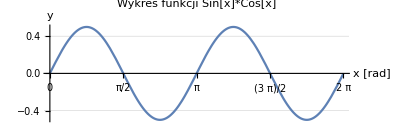

```mathematica
Plot[{Sin[x]*Cos[x]},{x,0,2*Pi},FrameLabel->{StyleForm["x",FontSize->10,Red],StyleForm["Funkcja",FontSize->10,Blue]},AxesLabel->{StyleForm["x [rad]",FontSize->12,Red],StyleForm["y",FontSize->12,Blue]},PlotLabel->StyleForm["Wykres funkcji Sin[x]*Cos[x]",12,Bold],GridLines->Automatic,Ticks->{Range[0,2 Pi,Pi/4],Automatic},AspectRatio->1/3]
```

```mathematica
(*Zadanie 2*)
```

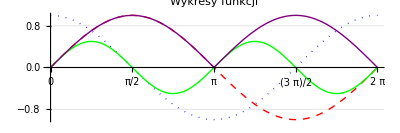

```mathematica
Plot[{Sin[x],Cos[x],Sin[x]*Cos[x],Abs[Sin[x]]},{x,0,2 Pi},PlotStyle->{{Red,Dashed,Thick},{Blue,Dotted,Thick},{Green,Thick},{Purple,Thick}},FrameLabel->{StyleForm["x",FontSize->12,Red],StyleForm["y",FontSize->12,Blue]},PlotLabel->StyleForm["Wykresy funkcji",14,Bold],GridLines->Automatic,Ticks->{Range[0,2 Pi,Pi/2],Automatic},AspectRatio->1/3,PlotLegends->Placed[LineLegend[{StyleForm["sin(x)",FontSize->12,Red],StyleForm["cos(x)",FontSize->12,Blue],StyleForm["sin(x)cos(x)",FontSize->12,Green],StyleForm["|sin(x)|",FontSize->12,Purple]},LegendLayout->"Row",LabelStyle->{FontSize->12}],{0.85,0.85}]]
```

```mathematica
(*zadanie 3*)
```

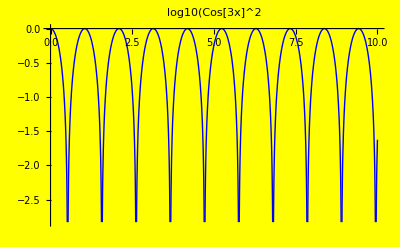

```mathematica
Plot[Log10[Cos[3 x]^2],{x,0,10},PlotStyle->Directive[Thick,Blue],FrameLabel->{None,StyleForm["log10(Cos[3x]^2)",FontSize->14]},PlotLabel->StyleForm["log10(Cos[3x]^2",FontSize->16,Bold,Red],Background->Yellow]
```

```mathematica
(*zadanie 4*)
```

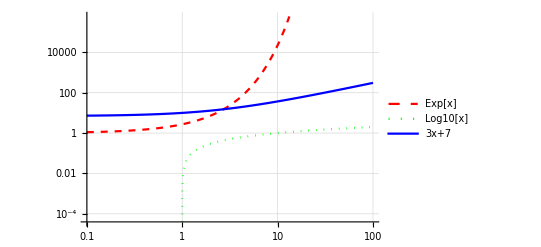

```mathematica
LogLogPlot[{Exp[x],Log10[x],3 x+7},{x,0.1,100},PlotStyle->{Directive[Red,Dashed],Directive[Green,Dotted],Directive[Blue,Thick]},GridLines->Automatic,FrameLabel->{StyleForm["log10(x)",FontSize->14,Red],StyleForm["log10(y)",FontSize->14,Blue]},PlotLegends->{"Exp[x]","Log10[x]","3x+7"}]
```

```mathematica
(*Zadanie 5*)
```

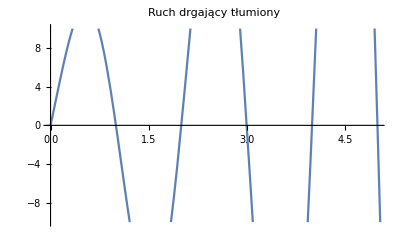

```mathematica
Plot[10*Exp[0.4*t]*Sin[Pi*t],{t,0,10},PlotRange->{{0,5},{-10,10}},FrameLabel->{StyleForm["czas (s)",FontSize->14,Red],StyleForm["pozycja (m)",FontSize->14,Blue]},PlotLabel->"Ruch drgający tłumiony"]
```

```mathematica
(*zadanie 6*)
```

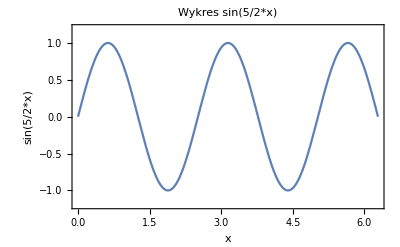

```mathematica
Plot[Sin[5/2*x],{x,0,2*Pi},PlotRange->{-1.2,1.2},Frame->True,FrameLabel->{StyleForm["x",FontSize->14,Red],StyleForm["sin(5/2*x)",FontSize->14,Blue]},PlotLabel->"Wykres sin(5/2*x)"]
```

```mathematica
(*zadanie 7*)
```

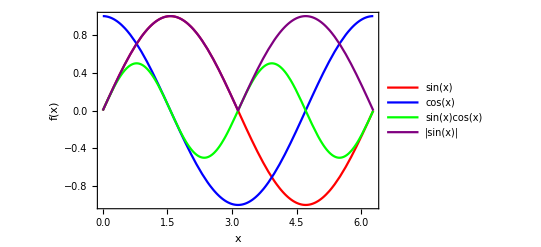

```mathematica
Plot[{Sin[x],Cos[x],Sin[x] Cos[x],Abs[Sin[x]]},{x,0,2*Pi},PlotStyle->{Red,Blue,Green,Purple},Frame->True,FrameLabel->{StyleForm["x",FontSize->14,Red],StyleForm["f(x)",FontSize->14,Blue]},PlotLegends->{"sin(x)","cos(x)","sin(x)cos(x)","|sin(x)|"}]
```

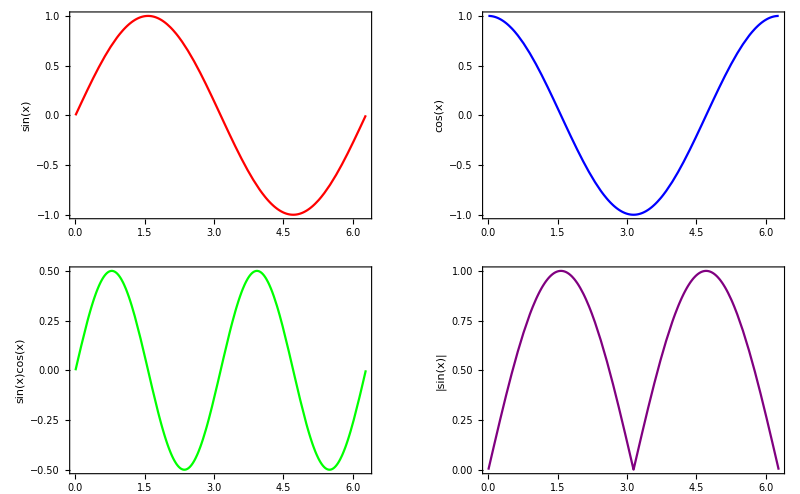

```mathematica
GraphicsGrid[{{Plot[Sin[x],{x,0,2*Pi},PlotStyle->Red,Frame->True,FrameLabel->{None,StyleForm["sin(x)",FontSize->14,Blue]}],Plot[Cos[x],{x,0,2*Pi},PlotStyle->Blue,Frame->True,FrameLabel->{None,StyleForm["cos(x)",FontSize->14,Blue]}]},{Plot[Sin[x] Cos[x],{x,0,2*Pi},PlotStyle->Green,Frame->True,FrameLabel->{None,StyleForm["sin(x)cos(x)",FontSize->14,Blue]}],Plot[Abs[Sin[x]],{x,0,2*Pi},PlotStyle->Purple,Frame->True,FrameLabel->{None,StyleForm["|sin(x)|",FontSize->14,Blue]}]}}]
```

```mathematica
(*zadanie 8*)
```

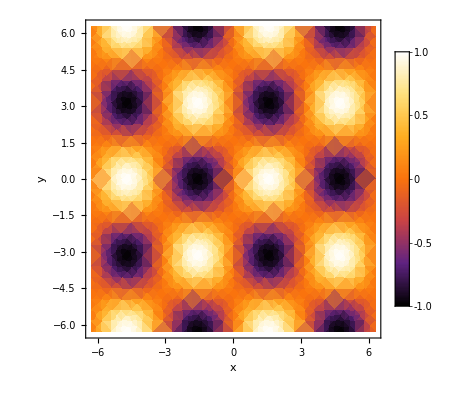

-Graphics3D-

```mathematica
DensityPlot[Sin[x]*Cos[y],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},PlotRange->All,ColorFunction->"SunsetColors",FrameLabel->{"x","y"},PlotLegends->Automatic]
Plot3D[Sin[x]*Cos[y],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},PlotRange->All,AxesLabel->{"x","y","f(x,y)"},ContourStyle->None]
```

```mathematica
(*a*)
```

```mathematica
Plot3D[Sin[x] Cos[y],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},Mesh->None,ColorFunction->None]
```

-Graphics3D-

```mathematica
(*b*)
```

```mathematica
Plot3D[Sin[x]*Cos[y],{x,-2 Pi,2 Pi},{y,-2 Pi,2 Pi},AxesLabel->{"x","y","z"},PlotPoints->100,PlotTheme->None,Mesh->None,ViewPoint->{0,0,Infinity}]
```

-Graphics3D-

```mathematica
(*zadanie 10*)
```

```mathematica
ParametricPlot3D[{Cos[t]*Sin[t],Sin[t]*Cos[u],Sin[u]},{t,0,2 Pi},{u,-Pi,Pi}]
```

```mathematica
ParametricPlot3D[{Cos[t]*Sin[t],Sin[t]*Cos[u],Sin[u]},{t,0,2 Pi},{u,-Pi,Pi},PlotRange->All,Axes->None,Boxed->False,ViewVector->{5,5,2},ViewAngle->0.3,ImageSize->Large]
```

-Graphics3D-

```mathematica
(*Zadanie 11*)
```

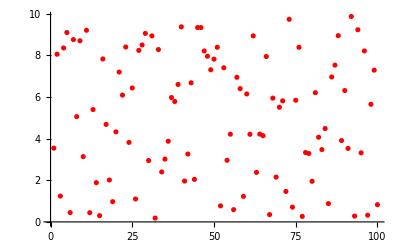

```mathematica
data=RandomReal[{0,10},100];
ListPlot[data,PlotStyle->Red,AxesOrigin->{0,0}]
```

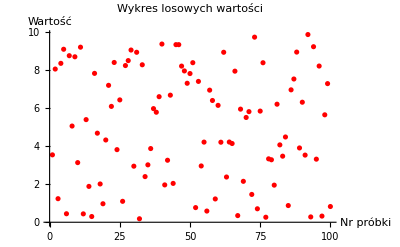

```mathematica
ListPlot[data,PlotStyle->Red,AxesOrigin->{0,0},AxesLabel->{"Nr próbki","Wartość"},PlotLabel->"Wykres losowych wartości"]
```

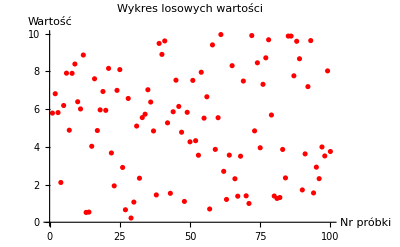

```mathematica
data=RandomReal[{0,10},100];
ListPlot[data,PlotStyle->Red,AxesOrigin->{0,0},AxesLabel->{"Nr próbki","Wartość"},PlotLabel->"Wykres losowych wartości"]
```

```mathematica
(*zadanie 12*)
```

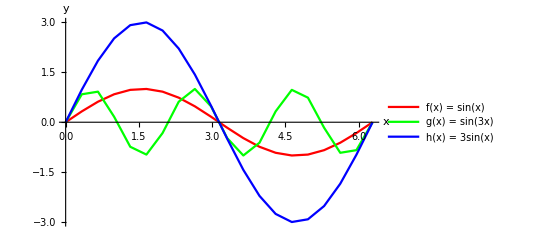

```mathematica
f[x_]:=Sin[x]
g[x_]:=Sin[3 x]
h[x_]:=3 Sin[x]

points=Table[{x,f[x]},{x,0,2 Pi,2 Pi/19}];
points2=Table[{x,g[x]},{x,0,2 Pi,2 Pi/19}];
points3=Table[{x,h[x]},{x,0,2 Pi,2 Pi/19}];

ListLinePlot[{points,points2,points3},PlotStyle->{Red,Green,Blue},Joined->True,PlotRange->All,AxesLabel->{"x","y"},PlotLegends->{"f(x) = sin(x)","g(x) = sin(3x)","h(x) = 3sin(x)"}]
```

```mathematica
(*zadanie 13*)
```

```mathematica
(*Definiujemy funkcję sinus*)f[x_]:=Sin[x]

(*Tworzymy listę wartości funkcji dla argumentów od 0 do 2Pi*)
values=Table[f[x],{x,0,2Pi,0.1}];

(*Tworzymy animację*)
Animate[ListLinePlot[values[[1;;n]],PlotRange->{-1,1}],{n,1,Length[values],1}]
```

```mathematica
(*zadanie 14*)
```

```mathematica
(*Ustawienia parametrów*)duration=1;(*czas trwania dźwięku w sekundach*)sampleRate=44100;(*liczba próbek na sekundę*)freqs={440,880,1760};(*częstotliwości dźwięków w Hz*)amps={0.3,0.6,0.9};(*amplitudy dźwięków*)(*Generowanie dźwięków*)sounds=Table[amp Sin[2 Pi freq t],{freq,freqs},{amp,amps},{t,0,duration,1/sampleRate}];

(*Odtwarzanie dźwięków*)
Sound[Flatten[sounds,2]]
```

Sound[{0.,0.0187945,0.0375152,0.0560884,0.0744414,0.0925018,396897,-0.855155,-0.758794,-0.61497,-0.432679,-0.223324,0.}]
 |  |  |  |

```mathematica
(*zadanie 15*)
```

```mathematica
frequencies={440,523.25,659.25,783.99};
amplitudes={0.7,0.5,0.3,0.1};

sound=Sum[amplitudes[[i]]*Sin[23*Pi*frequencies[[i]]*t],{i,1,Length[frequencies]}];

Play[sound,{t,0,1}]
```

-Graphics-

```mathematica
Play[sound]
```

Play::argr: Play called with 1 argument; 2 arguments are expected.

```mathematica
frequencies={440,523.25,659.25,783.99};
amplitudes={0.7,0.5,0.3,0.1};

sound=Sum[amplitudes[[i]]*Sin[23*Pi*frequencies[[i]]*t],{i,1,Length[frequencies]}];

Play[sound,{t,0,1}]
```

```mathematica
-Graphics-
Play[sound]
```

-Graphics-

Play::argr: Play called with 1 argument; 2 arguments are expected.

Play[sound]